## Mathematical Analysis Problem Set 8

## Problems For Thursday, May 13, 2021 — the reading is to finish Chapter 6

## Limits and Composition of Functions

### 1(a)

Hopefully, you vaguely remember this handout from before the break. We are trying to gain intuition about how limits work when functions are composed, in this case f(g(x)) at x=2. Below, I have changed the function slightly from the last handout (made it sin(π x) instead of sin(x)), and also blown up the region from x=15 to x=17.

```mathematica
f[x_]:=Sin[Pi x]
```

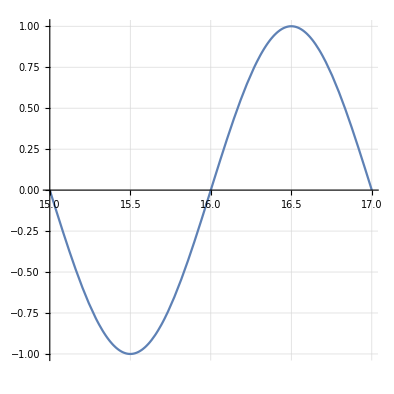

```mathematica
Plot[f[x],{x, 15, 17}, PlotRange->{{15, 17}, {-1, 1}}, GridLines->Automatic,AspectRatio->1.0]
```

When x=16, sin(π x)=0. Estimate by using a straight edge, how much can x change and sin(π x) still be within 1/2 of 0? (You can also figure this out algebraically and exactly using that sin(π/6)=1/2.

### 1(b)

We are going to compose this with x^4. So we will be considering sin(π x^4) near x=2.

To help you be more exact in what you are about to do, I have blown up g(x) near x=2. The function is very steep.

```mathematica
g[x_]:=x^4
```

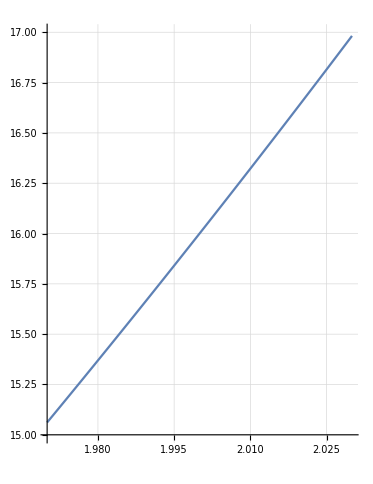

```mathematica
Plot[g[x],{x,1.97, 2.03}, PlotRange->{{1.97,2.03}, {15, 17}}, GridLines->Automatic, AspectRatio->1.3]
```

What you want to do is take the range of x values that you found in 1(a). We want to know the x range on this plot that keeps x^4 within the range you found  in 1(a). Do that with a straight edge.

### 1(c)

Now we will check our work. I have graphed the composition of the functions. Using the range of x values you found in 1(b), is the composition of the functions within 1/2 of 0 at x=2 for that range?

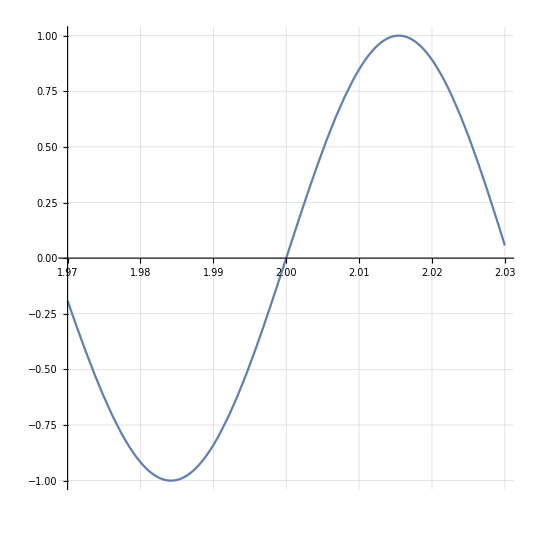

```mathematica
Plot[f[g[x]],{x, 1.97, 2.03}, PlotRange->{{1.97, 2.03}, {-1, 1}}, GridLines->Automatic, MaxRecursion->15, AspectRatio->1.0]
```

## 2 Problems that are like Problem 6 on the Exam

Here are  two more problems to be solved with the same techniques as Problem 6 on the exam. If necessary, grab the exam solution to remind yourself how these are typically done.

For both limits below, first, what is the limit? Second, for ϵ > 0,  what is the δ that keeps the function within ϵ of the limit.

### 2(a)

```mathematica
1/x^3x1
```

### 2(b)

```mathematica
With a>0,1/x^2xa
```

## 3 More Problems that are like Problem 6 on the Exam

More problems that are good practice for Problem 6 on the exam are all parts of Spivak Problem 3 of Spivak Chapter 5.

### (i)-(vi)

I don't like to burden you guys with too much work, but we really have to hammer this in until it is just obvious what to do every time you encounter one of these, so do all six parts. If there is one thing to take away from this entire course, and that will put you in good stead when you hit calculus, it is proving limits for whatever miscellaneous functions you encounter.

## Good Elementary Proofs for in-class on Thursday

Thursday’s reading is to finish Chapter 6 (before the break you did to p. 115). The remaining two pages of the chapter are dense. You should try to prove the following two things before class.

### (a) For in-class on Thursday, a proof related to Problem 7 on the exam

In problem 7, I tried for the easiest proof involving limits that I could come up with. The δ' that worked in the second limit was 2δ.

A harder version of Problem 7 would be to show that the following two limits (if one exists), must be equal, and find the δ that makes it so.

So, assume this exists:

```mathematica
l=f(x)x0
```

Write out what it means for the above limit to exist.

From that, prove that the following limit exists and is also l. You will once again be finding a δ' that is related to δ. If you don’t know what to do, maybe construct an interesting example to present instead of a proof?

```mathematica
f(x^2)x0
```

### (b) Also for in-class on Thursday, a proof that gets us into the material of Chapter 6

Finally, for class on Thursday, let’s tackle Problem 3 from Chapter 6.